# ASTR 510 - HW 1

## Daniel George

## Q2

### Stencil for 4th order centered derivative

```mathematica
st4={-1,8,0,-8,1}/12;
```

### Expression for 4th order centered derivative

```mathematica
d4q=(st4/dx) . q[n]/@Range[i+2,i-2,-1]
```

(q[n][-2+i])/(12 dx)-(2 q[n][-1+i])/(3 dx)+(2 q[n][1+i])/(3 dx)-(q[n][2+i])/(12 dx)

### 4th order FTCS scheme for the advection equation

```mathematica
ftcs4=(q[n+1][i]-q[n][i])/dt + a d4q==0
```

a ((q[n][-2+i])/(12 dx)-(2 q[n][-1+i])/(3 dx)+(2 q[n][1+i])/(3 dx)-(q[n][2+i])/(12 dx))+(-q[n][i]+q[1+n][i])/dt==0

### Trial solution for von Neumann stability analysis

```mathematica
trial=q[n_][j_]->ξ^n Exp[I k j];
```

### Substituting it in the FTCS scheme

```mathematica
eq=ftcs4/.trial
```

a ((ⅇ^(ⅈ (-2+i) k) ξ^n)/(12 dx)-(2 ⅇ^(ⅈ (-1+i) k) ξ^n)/(3 dx)+(2 ⅇ^(ⅈ (1+i) k) ξ^n)/(3 dx)-(ⅇ^(ⅈ (2+i) k) ξ^n)/(12 dx))+(-ⅇ^(ⅈ i k) ξ^n+ⅇ^(ⅈ i k) ξ^(1+n))/dt==0

### Solving for ξ

```mathematica
sol=Solve[eq,ξ][[1]]//FullSimplify
```

{ξ→1+(ⅈ a dt (-4+Cos[k]) Sin[k])/(3 dx)}

## a)

### Calculating Dissipation Error = 1-|ξ|

```mathematica
dissE[σ_]=1-Abs[ξ]/.sol/.{dt->σ dx/a}
```

1-Abs[1+1/3 ⅈ σ (-4+Cos[k]) Sin[k]]

### Plot of dissipation error vs σ

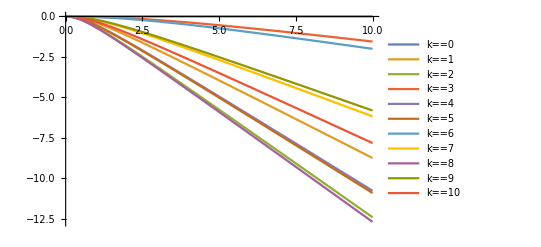

```mathematica
Plot[Evaluate@Table[dissE[σ]/.{k->k1},{k1,0,10,1}],{σ,0,10},PlotLegends->Table[k==k1,{k1,0,10}]]
```

It  can be observed that for all values of k ≠ 0 the dissipation error increases monotonically with σ. It is always greater than 1.

## b)

### Calculating Dispersion Error = 1 + arg(ξ) / (k σ)

```mathematica
dispE[σ_]=1+Arg[ξ]/(k σ)/.sol/.{dt->σ dx/a}
```

1+Arg[1+1/3 ⅈ σ (-4+Cos[k]) Sin[k]]/(k σ)

### Plot of dispersion error vs σ

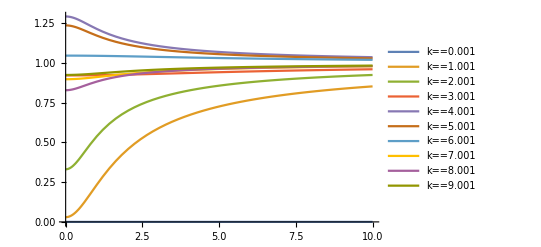

```mathematica
Plot[Evaluate@Table[dispE[σ]/.{k->k1},{k1,0.001,10}],{σ,0,10},PlotLegends->Table[k==k1,{k1,0.001,10}],PlotRange->All]
```

It can be observed by varying the values of k that the dispersion error always remains bounded. The dispersion error increases monotonically and asymptotically tends to 1 for all values of k.

## c)

### The method is stable if dissipation error is less than 1

```mathematica
Reduce[1-dissE[σ]≤1&&k≥0&&σ>0,σ]
```

C[1]∈Integers&&C[1]≥0&&((k==π+2 π C[1]&&σ>0)||(k==2 π C[1]&&σ>0))

Thus the mehod is stable only when k = n π. Therefore the method is conditionally stable.

## Q1

## f)

### Number of cores used

```mathematica
nP={1,2,4,8,12,24,36};
```

### Grid sizes used

```mathematica
nG={200,400,1600};
```

### Time taken for grid size = 200

```mathematica
time[200][1]=4.5407269001007080;
time[200][2]=2.2643110752105713;
time[200][4]=1.0853230953216553;
time[200][8]=0.67126584053039551;
time[200][12]=0.65181708335876465;
time[200][24]=9.5089979171752930;
time[200][36]=9.6296432018280029;
```

### Time taken for grid size = 400

```mathematica
time[400][1]=69.583978891372681;
time[400][2]=36.501708030700684;
time[400][4]=26.051327943801880;
time[400][8]=15.519846916198730;
time[400][12]=21.609544992446899;
time[400][24]=78.850456953048706;
time[400][36]=79.048186063766479;
```

### Time taken for grid size = 1600

```mathematica
time[1600][1]=27739.625624895096;
time[1600][2]=20571.754885911942;
time[1600][4]=19038.544435977936;
time[1600][8]=12406.615384101868;
time[1600][12]=5006.3509409427643;
time[1600][24]=4432.3666520118713;
time[1600][36]=2335.3625159263611;
```

## g)

### Log-linear plots of time vs number of cores for each grid size

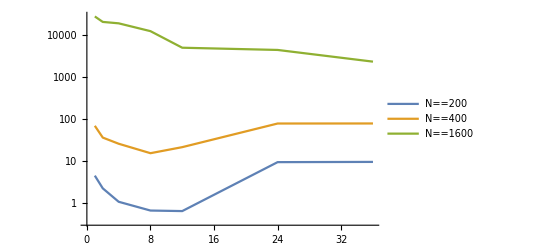

```mathematica
ListLogPlot[Function[n,Transpose[{#,time[n]/@#}]&@nP]/@nG,Joined->True,PlotLegends->Table[N==i,{i,nG}]]
```

### Log-linear plots of parallel efficiency vs number of cores

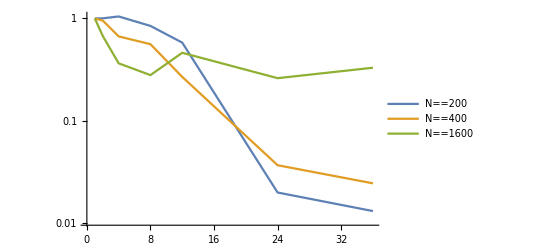

```mathematica
ListLogPlot[Function[n,Transpose[{#,time[n][1]/(#*(time[n]/@#))}]&@nP]/@nG,Joined->True,PlotLegends->Table[N==i,{i,nG}]]
```

It can be observed that there are deviations from ideal scaling i.e. parallel efficiency decreases from 1 as number of cores increase, especially when number of grid points are small. The main reason for the decrease in parallel efficiency seems to be load imbalance since the parallel efficiency gets better for larger number of grid points. Other factors such as communication delays, data/control dependencies, etc. could also further decrease the parallel efficiency.

## h)

### Time taken for a single processor vs grid points

```mathematica
coretimes=Transpose[{nG,time[#][1]&/@nG}]
```

{{200,4.54073},{400,69.584},{1600,27739.6}}

### Log-log plot of time vs grid points

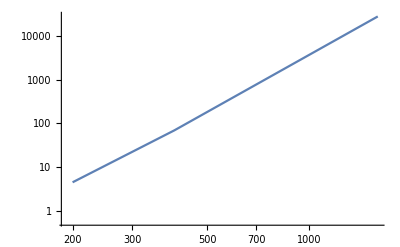

```mathematica
ListLogLogPlot[coretimes,Joined->True]
```

Thus it can be seen that the log-log plot of the data is almost a straight line. Therefore it can be extrapolated to estimate the core hours required for a 3200x3200 grid.

### Finding a formula by extrapolating the log of the data

```mathematica
ft[x_]=Fit[Log@coretimes,{1,x},x]
```

-20.8707+4.21042 x

### Estimate for time required for 3200x3200 grid

```mathematica
UnitConvert[Exp@ft[Log[3200]]Quantity[, "Seconds"],"Hours"]
```

137.355 h

Thus based on the data it would take about 137 core-hours for the calculation on a 3200x3200 grid assuming maximum parallel efficiency.

With up to 32 processors we can see that the total time taken decreases with increase in number of processors. Therefore we expect for a 3200x3200 we should be able to use as many processors as are available in the cluster to run a feasible calculation. (Although with too many processors the time may increase but this cannot be inferred from the data available).

## i)

### Importing data from mheat.out file

```mathematica
data=Partition[Flatten@Import["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR510\\mheat.txt","Table"],400];
```

### Creating a contour plot of the temperature field

```mathematica
ListContourPlot[data,Contours->10,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics-